```mathematica
ClearAll["Global`*"]
```

```mathematica
tag ={"#boston","#bostonmarathon","#bostonstrong","#prayforboston"};
TagType ={"#boston","#bostonmarathon","#bostonstrong","#prayforboston"};
PlotType={VC,VID,CC,GD,GR,GCC,GA,MND,MDC};
S[x_]:=StringSplit[StringReplace[x,{"\""->""}]," -> "];
Fdate[x_]:=DateString[{2013,4,15,6,((i-1)*10),0},{"DayNameShort","Hour12","Minute","AMPMLowerCase"}];
FFdate[x_]:=DateString[{2013,4,15,(5+x/10),0,0},{"DayNameShort","Hour12","AMPMLowerCase"}];
```

```mathematica
L=576;
n=3;(*selects the third hashtag*)
For[i=1,i≤L,i++,

file="/Users/danielgladstone/Documents/twitter_project/auto_graphing/#bostonstrong_d4_l2/"<>Fdate[i];

If[FileExistsQ[file],

F =Import[file,"List"];

GList[i]=DeleteDuplicates[Table[
joined=First[S[F[[j]]]]->Last[S[F[[j]]]]
,{j,1,Length[F]}]];

If[Length[GList[i]]≤1,

(*Print["Zero: n="<>ToString[n]<>". i="<>ToString[i]];*)

G[i]=0;
G[VC][i]=0;
G[VID][i]=0;
G[CC][i]=0;
G[GD][i]=0;
G[GR][i]=0;
G[GCC][i]=0;
G[GA][i]=0;
G[MND][i]=0;
G[MDC][i]=0;,

G[i]=Graph[GList[i]];
G[VC][i]=VertexCount[G[i]];
G[VID][i]=Mean[VertexInDegree[G[i]]];
G[CC][i]=Mean[ClosenessCentrality[G[i]]];
G[GD][i]=GraphDensity[G[i]];
G[GR][i]=GraphReciprocity[G[i]];
G[GCC][i]=GlobalClusteringCoefficient[G[i]];
G[GA][i]=GraphAssortativity[G[i]];
G[MND][i]=Mean[MeanNeighborDegree[G[i]]];
G[MDC][i]=Mean[MeanDegreeConnectivity[G[i]]];
];
,
G[i]=0;
G[VC][i]=0;
G[VID][i]=0;
G[CC][i]=0;
G[GD][i]=0;
G[GR][i]=0;
G[GCC][i]=0;
G[GA][i]=0;
G[MND][i]=0;
G[MDC][i]=0;]
]
```

```mathematica
For[p=1,p≤9,p++,(*iterate over each data type*)

GT=PlotType[[p]];

data=
Table[
Table[
T=tag[[3]];(*What hashtag are we looking at*)
G[GT][i],{i,L}] (*Iterate over every time period*)
,{n,3,3}]; (*Iterate over each hashtag*)

Data[p]=data; (*list of data for a given graph type in with composed of smaller list for each hashtag*)
]
```

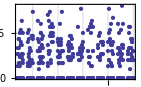
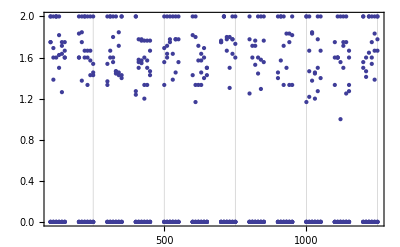
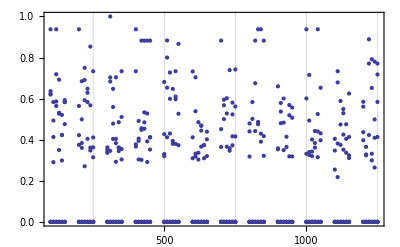
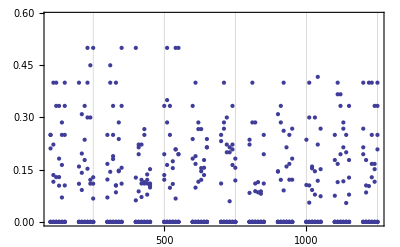
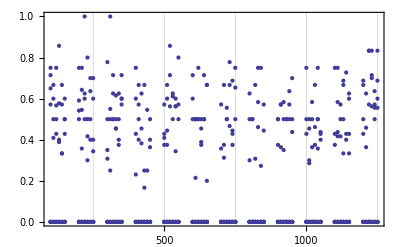
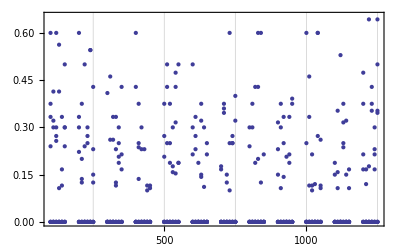
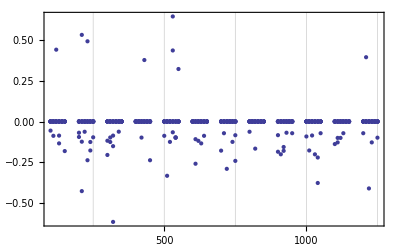
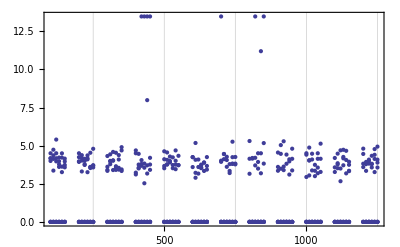

```mathematica
For[p=1,p≤9,p++,
dt[p]=
Table[
{Fdate[i],Data[p][[1]][[i]]}
,{i,L}];]
bpd=Table[DateListPlot[dt[p],{Fdate[1],Fdate[L]}],{p,9}]
```

```mathematica
Data[1][[1]][[1]]
```

0

```mathematica
lp=Table[ListPlot[Data,PlotLabel->type[[o]], PlotLegends->Table[
tag[[t]],{t,1,4}]]
,{o,9}];
```